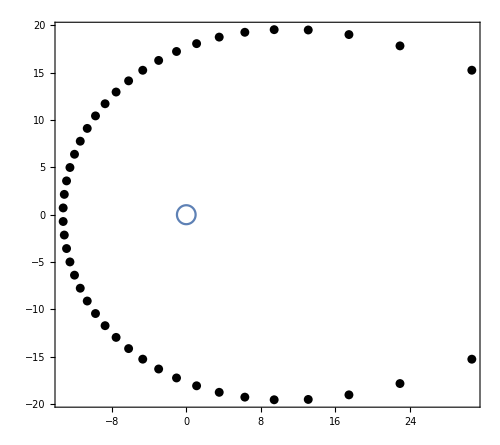

```mathematica
p[n_,z_]:=Sum[z^k/k!,{k,0,n}];
Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[44,z]==0,z],PlotStyle->{Black,Thick}],
PlotRange->All,Axes->False,Frame->True,ImageSize->500]
```

```mathematica
Solve[1+z+z^2/2==0,z]
```

{{z→-1-ⅈ},{z→-1+ⅈ}}

```mathematica
Grid[{{Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[4,z]==0,z],PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-4.4,4.4},{-4.4,4.4}},Axes->False,Frame->True,ImageSize->300],Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[5,z]==0,z],PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-4.4,4.4},{-4.4,4.4}},Axes->False,Frame->True,ImageSize->300]},{Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[6,z]==0,z],PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-4.4,4.4},{-4.4,4.4}},Axes->False,Frame->True,ImageSize->300],Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[7,z]==0,z],PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-4.4,4.4},{-4.4,4.4}},Axes->False,Frame->True,ImageSize->300]}}]
```

```mathematica
Export["d4thru7.png",-Graphics-]
```

d4thru7.png

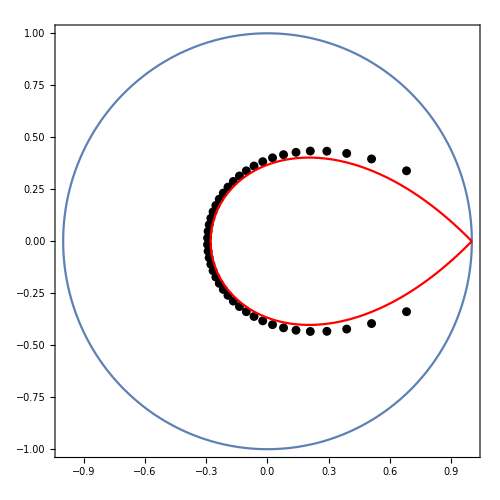

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[44,45 z]==0,z],PlotStyle->Black],
ContourPlot[(x^2+y^2) E^(2-2 x)==1,{x,-1,1},{y,-1,1},ContourStyle->Red,PlotPoints->60],
PlotRange->All,Axes->False,Frame->True,ImageSize->500]
```

```mathematica
a=0.01;
zeros={Re[z],Im[z]}/.Solve[(1+3 z) (z-(I-0.6)/3) (z-(0.7-I/2)/2)==0,z];
crosses1=Table[{zeros[[j]],zeros[[j]]}+{{-a,-a},{a,a}},{j,1,Length[zeros]}];
crosses2=Table[{zeros[[j]],zeros[[j]]}+{{-a,a},{a,-a}},{j,1,Length[zeros]}];
graphicscontents={AbsoluteThickness[2]}~Join~Table[Line[crosses1[[j]]],{j,1,1}]~Join~Table[Line[crosses2[[j]]],{j,1,1}];
```

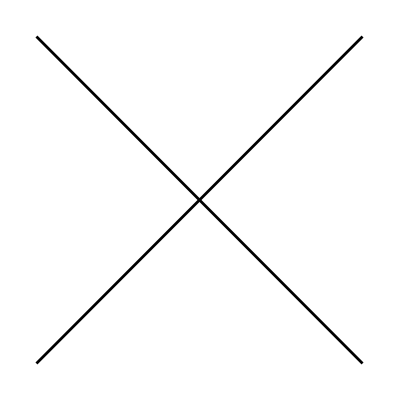

```mathematica
Show[Graphics[graphicscontents]]
```

0.0670341+0.387632 ⅈ

-1.01193

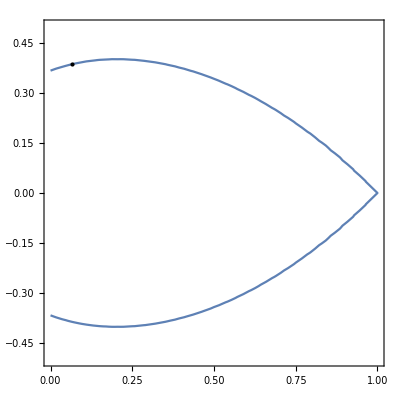

```mathematica
θ=Pi/2-Pi 15/100+3/10;
ξ=r E^(I θ)/.FindRoot[r E^(1-r Cos[θ])==1,{r,0.7}]
τ=Im[ξ-1-Log[ξ]]
τn[n_]:=Mod[τ n,2 Pi,-Pi];
Show[
ContourPlot[(x^2+y^2) E^(2-2 x)==1,{x,0,1},{y,-1/2,1/2},AspectRatio->1],
Graphics[Point[{Re[ξ],Im[ξ]}]]
]
```

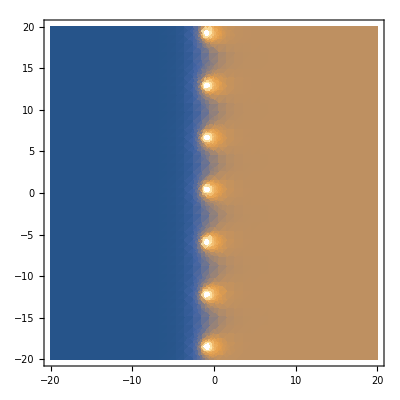

```mathematica
DensityPlot[1/Abs[1-E^(-x-I y)/Sqrt[2 Pi]/(1-ξ)],{x,-20,20},{y,-20,20},PlotPoints->40]
```

```mathematica
Subscript[w2, 1]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,0}]
Subscript[w2, 2]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,6 I}]
Subscript[w2, 3]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,12 I}]
Subscript[w2, 4]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,-6 I}]
Subscript[w2, 5]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,-12 I}]
Subscript[w2, 6]=w/.FindRoot[1-E^(-w)/Sqrt[2 Pi]/(1-ξ),{w,-20 I}]
```

-0.929175+0.393782 ⅈ

-0.929175+6.67697 ⅈ

-0.929175+12.9602 ⅈ

-0.929175-5.8894 ⅈ

-0.929175-12.1726 ⅈ

-0.929175-18.4558 ⅈ

```mathematica
m=45;
z2[j_]:=ξ (1+Log[m]/(2 (1-ξ) m)-(Subscript[w2, j]-I τn[m])/(1-ξ)/m);
```

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]}/5,{t,0,2 Pi},PlotStyle->Opacity[0]],
ListPlot[{Re[z],Im[z]}/.NSolve[p[m-1,m z]==0,z,WorkingPrecision->20],PlotStyle->Black],
ContourPlot[(x^2+y^2) E^(2-2 x)==1,{x,-1,1},{y,-1,1},ContourStyle->Red,PlotPoints->60],
ListPlot[Table[{Re[z2[k]],Im[z2[k]]},{k,1,6}],PlotMarkers->Graphics[{graphicscontents},ImageSize->16],PlotStyle->Blue],
Graphics[{PointSize[0.012],Blue,Point[{Re[ξ],Im[ξ]}]}],
PlotRange->{-1/10,1/2},Axes->False,Frame->True,ImageSize->720]
```

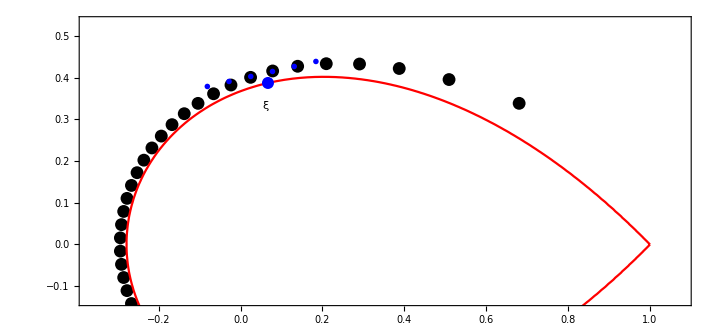

```mathematica
zz[n_,w_]:=ξ (1+Log[n]/(2 (1-ξ) n)-(w-I τn[n])/(1-ξ)/n);
```

```mathematica
m=100;
rangex=15;rangey=15;
```

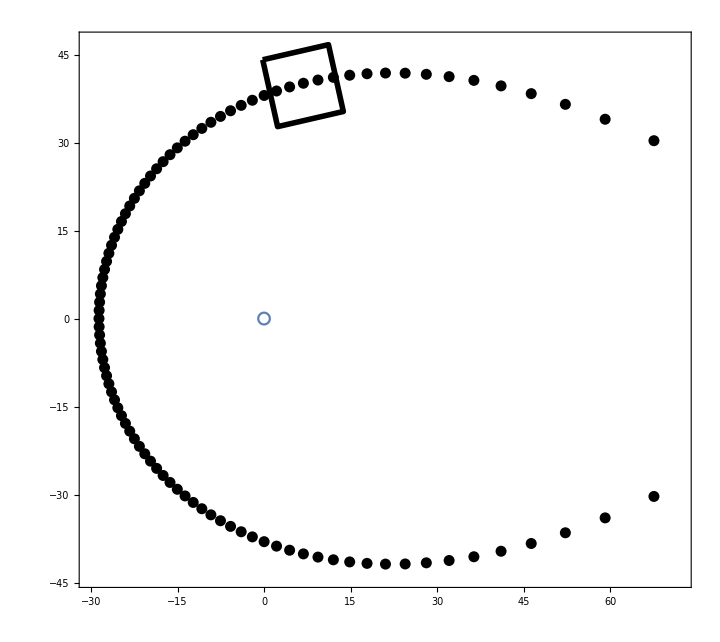

```mathematica
Show[ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],ListPlot[{Re[z],Im[z]}/.NSolve[p[m-1,z]==0,z,WorkingPrecision->20],PlotStyle->Black],Graphics[{EdgeForm[{AbsoluteThickness[4],Black}],FaceForm[],Polygon[{m {Re[zz[m,-rangex-rangey I]],Im[zz[m,-rangex-rangey I]]},m {Re[zz[m,rangex-rangey I]],Im[zz[m,rangex-rangey I]]},m {Re[zz[m,rangex+rangey I]],Im[zz[m,rangex+rangey I]]},m {Re[zz[m,-rangex+rangey I]],Im[zz[m,-rangex+rangey I]]}}]}],PlotRange->{{-30,72},{-44,47}},Axes->False,Frame->True,ImageSize->720]
```

```mathematica
m=.;
```

```mathematica
images=Table[Show[ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],ListPlot[{Re[z],Im[z]}/.NSolve[p[m-1,z]==0,z,WorkingPrecision->20],PlotStyle->Black],Graphics[{EdgeForm[{AbsoluteThickness[4],Black}],FaceForm[],Polygon[{m {Re[zz[m,-rangex-rangey I]],Im[zz[m,-rangex-rangey I]]},m {Re[zz[m,rangex-rangey I]],Im[zz[m,rangex-rangey I]]},m {Re[zz[m,rangex+rangey I]],Im[zz[m,rangex+rangey I]]},m {Re[zz[m,-rangex+rangey I]],Im[zz[m,-rangex+rangey I]]}}]}],PlotRange->{{-30,72},{-44,47}},Axes->False,Frame->True,ImageSize->720],{m,20,100,1}];
```

```mathematica
Export["scalinglimit.gif",images,"DisplayDurations"->1/10]
```

scalinglimit.gif